# 飓风球

## 准备工作

转动惯量和拉氏量的说明：

```mathematica
Clear[M,R,g,μ,para,T,V,energy,L];
para={M->1,R->1,g->1,μ->.1};
para={M->20 10^-3,R->8.5 10^-3,g->9.8,μ->.1,μr->.005,ρ->1.29,c->.01};
tmax=45;
{I1,I2,I3}={14/5,14/5,4/5}M R^2;
z[t_]=R(1+Cos@θ[t]);
T=1/2 I1 ϕ'[t]^2 Sin[θ[t]]^2+1/2 I2 θ'[t]^2+1/2 I3(ψ'[t]+ϕ'[t]Cos[θ[t]])^2+1/2*2M z'[t]^2;
V=2M g z[t];
energy=T+V;
L=T-V
```

-2 g M R (1+Cos[θ[t]])+7/5 M R^2 θ'[t]^2+M R^2 Sin[θ[t]]^2 θ'[t]^2+7/5 M R^2 Sin[θ[t]]^2 ϕ'[t]^2+2/5 M R^2 (Cos[θ[t]] ϕ'[t]+ψ'[t])^2

图元

```mathematica
hurriballs[θ_,ϕ_,ψ_,R_:1]:={Ball[R{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},R],Ball[-R{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},R]};
arrows[θ_,ϕ_,ψ_,R_:1]:={Arrow[{-3R{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},3R{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}}],Arrow[{{0,0,0},1.5R FullSimplify[RotationTransform[ϕ,{0,0,1}]@RotationTransform[ψ,{Sin[θ],0,Cos[θ]}]@RotationTransform[θ,{0,1,0}]@{-1,0,0},{θ,ψ,ϕ}∈Reals]}]};
```

示意图：

```mathematica
Manipulate[Graphics3D[Evaluate@{hurriballs[θ,ϕ,ψ],arrows[θ,ϕ,ψ],InfinitePlane[{{0,0,0},{0,1,0},{1,0,0}}-1-Cos[θ]]},PlotRange->{{-3,3},{-3,3},{-4-Cos[θ],4-Cos[θ]}}],{θ,0,π/2},{ϕ,0,2π},{ψ,0,2π}]
```

## 列方程与解方程：

外力条件（一定要重写方程！）：

滚动摩擦+滑动摩擦+空气阻力

```mathematica
Subscript[F, N]=2M g;
Mr=-μr Subscript[F, N] R Sin[θ[t]]-2c ρ π R^2 R^2 ϕ'[t]^2;
Subscript[Q, θ]=0;
Subscript[Q, ϕ]=Mr-μ Subscript[F, N] R Sin[θ[t]]Erf[100(ϕ'[t]-ψ'[t])];
Subscript[Q, ψ]=μ Subscript[F, N] R Sin[θ[t]]Erf[100(ϕ'[t]-ψ'[t])];
```

滚动摩擦、简化正压力、有滑动摩擦

```mathematica
Subscript[F, N]=2M g;
Mr=-μr Subscript[F, N] R Sin[θ[t]];
Subscript[Q, θ]=0;
Subscript[Q, ϕ]=Mr-μ Subscript[F, N] R Sin[θ[t]]Erf[100(ϕ'[t]-ψ'[t])];
Subscript[Q, ψ]=μ Subscript[F, N] R Sin[θ[t]]Erf[100(ϕ'[t]-ψ'[t])];
```

恒定动力、简化正压力、有摩擦

```mathematica
Subscript[F, N]=2M g;
Subscript[Q, θ]=0;
Subscript[Q, ϕ]=2 10^-5-μ Subscript[F, N] R Sin[θ[t]]Sign[ϕ'[t]-ψ'[t]];
Subscript[Q, ψ]=μ Subscript[F, N] R Sin[θ[t]]Sign[ϕ'[t]-ψ'[t]];
```

恒定空气阻力、简化正压力、有摩擦

```mathematica
Subscript[F, N]=2M g;
(*Subscript[F, N]=2M(g+D[R Cos[θ[t]],{t,2}]);*)
Subscript[Q, θ]=0;
Subscript[Q, ϕ]=-.5-μ Subscript[F, N] R Sin[θ[t]]Sign[ϕ'[t]-ψ'[t]];
Subscript[Q, ψ]=μ Subscript[F, N] R Sin[θ[t]]Sign[ϕ'[t]-ψ'[t]];
```

无动力、真实正压力（好像不大对）

```mathematica
Subscript[F, N]=2M(g+D[R Cos[θ[t]],{t,2}]);
Subscript[Q, θ]=0;
Subscript[Q, ϕ]=-μ Subscript[F, N] R Sin[θ[t]]Sign[ϕ'[t]-ψ'[t]];
Subscript[Q, ψ]=μ Subscript[F, N] R Sin[θ[t]]Sign[ϕ'[t]-ψ'[t]];
```

无动力、简化正压力的摩擦

```mathematica
Subscript[F, N]=2M g;
Subscript[Q, θ]=0;
Subscript[Q, ϕ]=-μ Subscript[F, N] R Sin[θ[t]]Sign[ϕ'[t]-ψ'[t]];
Subscript[Q, ψ]=μ Subscript[F, N] R Sin[θ[t]]Sign[ϕ'[t]-ψ'[t]];
```

无动力、单向摩擦（简化正压力）

```mathematica
Subscript[F, N]=2M g;
Subscript[Q, θ]=0;
Subscript[Q, ϕ]=-μ Subscript[F, N] R Sin[θ[t]];
Subscript[Q, ψ]=μ Subscript[F, N] R Sin[θ[t]];
```

最简情况：无动力、无摩擦

```mathematica
Subscript[F, N]=2M g;
Subscript[Q, θ]=0;
Subscript[Q, ϕ]=0;
Subscript[Q, ψ]=0;
```

列方程：

```mathematica
eqns=Table[FullSimplify[D[D[L,α'[t]],t]-D[L,α[t]]]==Subscript[Q, α],{α,{θ,ϕ,ψ}}]
```

{2/5 M R (Sin[θ[t]] (-5 g+5 R Cos[θ[t]] (θ'[t]^2-ϕ'[t]^2)+2 R ϕ'[t] ψ'[t])+R (7+5 Sin[θ[t]]^2) θ''[t])==0,1/5 M R^2 (4 Sin[θ[t]] θ'[t] (5 Cos[θ[t]] ϕ'[t]-ψ'[t])+(9-5 Cos[2 θ[t]]) ϕ''[t]+4 Cos[θ[t]] ψ''[t])==-2 g M R μr Sin[θ[t]]-2 g M R μ Erf[100 (ϕ'[t]-ψ'[t])] Sin[θ[t]]-2 c π R^4 ρ ϕ'[t]^2,4/5 M R^2 (-Sin[θ[t]] θ'[t] ϕ'[t]+Cos[θ[t]] ϕ''[t]+ψ''[t])==2 g M R μ Erf[100 (ϕ'[t]-ψ'[t])] Sin[θ[t]]}

设定初始条件：

```mathematica
θ0=67Degree;Subscript[ω, θ,0]=0;Subscript[ω, ϕ,0]=8;Subscript[ω, ψ,0]=6;
initc={θ[0]==θ0,θ'[0]==Subscript[ω, θ,0],ϕ[0]==0,ϕ'[0]==Subscript[ω, ϕ,0],ψ[0]==0,ψ'[0]==Subscript[ω, ψ,0]};
event={WhenEvent[Mod[ϕ[t],2π]==0,Sow[t,"periods"]],
WhenEvent[Evaluate[Subscript[F, N]<0],{Print["Warning! F_N<0 at t="<>ToString@t],Sow[t,"errortime"],"RemoveEvent"}],
WhenEvent[Evaluate[θ[t]>90 Degree],{Print["Warning! θ[t]>90° at t="<>ToString@t],Sow[t,"errortime"],"RemoveEvent"}]};
```

```mathematica
θ0=68Degree;Subscript[ω, θ,0]=0;Subscript[ω, ϕ,0]=180;Subscript[ω, ψ,0]=180;
(*θ0=ArcCos[2/5-g/(Subscript[ω, ϕ,0]^2 R)]/.para;*)
initc={θ[0]==θ0,θ'[0]==Subscript[ω, θ,0],ϕ[0]==0,ϕ'[0]==Subscript[ω, ϕ,0],ψ[0]==0,ψ'[0]==Subscript[ω, ψ,0]};
event={WhenEvent[Mod[ϕ[t],2π]==0,Sow[t,"periods"]],
WhenEvent[Evaluate[Subscript[F, N]<0],{Print["Warning! F_N<0 at t="<>ToString@t],Sow[t,"errortime"],"RemoveEvent"}],
WhenEvent[Evaluate[θ[t]>90 Degree],{Print["Warning! θ[t]>90° at t="<>ToString@t],Sow[t,"errortime"],"RemoveEvent"}]};
```

解方程

```mathematica
{{sol},{{periods},errortime}}=Reap[NDSolve[{eqns,initc,event}//.para,{θ[t],ϕ[t],ψ[t]},{t,0,tmax},InterpolationOrder->All],{"periods","errortime"}];sol
```

Warning! θ[t]>90° at t=33.3078

{θ[t]→InterpolatingFunction[{{0., 45.}}, <>][t],ϕ[t]→InterpolatingFunction[{{0., 45.}}, <>][t],ψ[t]→InterpolatingFunction[{{0., 45.}}, <>][t]}

## 绘图、分析

动态展示

```mathematica
Manipulate[Evaluate[Graphics3D[{hurriballs[θ[t],ϕ[t],ψ[t]],arrows[θ[t],ϕ[t],ψ[t]],InfinitePlane[{{0,0,0},{0,1,0},{1,0,0}}-1-Cos[θ[t]]]},
PlotRange->{{-3,3},{-3,3},{-3-Cos[θ[t]],3-Cos[θ[t]]}}]/.sol],{t,0,tmax}]
```

章动角θ-t 图

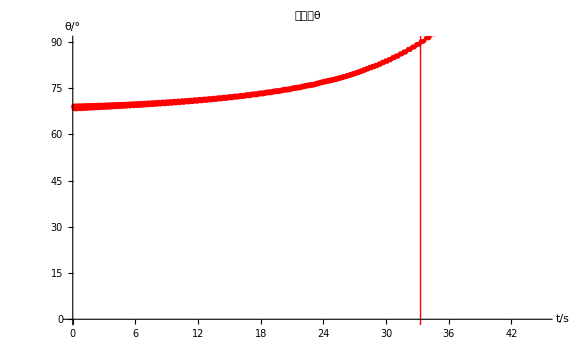

```mathematica
Plot[Evaluate@{{θ[t]}/Degree/.sol,ArcCos[2/5-g/(D[ϕ[t]/.sol,t]^2 R)/.para]/Degree},{t,0,tmax},PlotRange->{0,90},Epilog->{Red,PointSize[.005],Point[Table[{t,θ[t]/Degree}/.sol,{t,periods}]],Table[InfiniteLine[{t,0},{0,1}],{t,Flatten@errortime}]},PlotLabel->"章动角θ",AxesLabel->{"t/s","θ/°"},PlotPoints->200,ImageSize->Large]
```

角速度-时间图

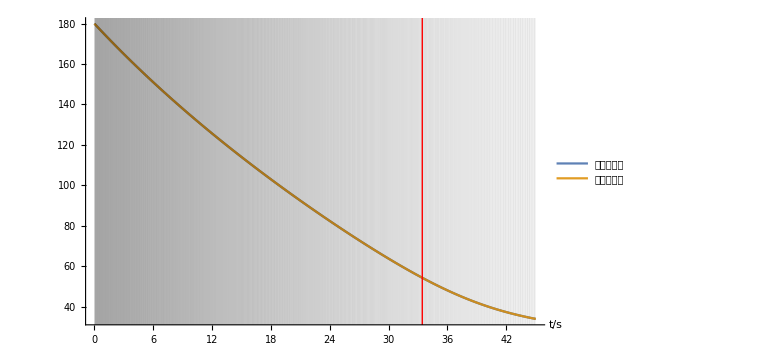

```mathematica
Plot[Evaluate[D[{ϕ[t],ψ[t]}/.sol,t]/.t->tn],{tn,0,tmax},
Epilog->{Opacity[.1],PointSize[.005],Table[InfiniteLine[{t,0},{0,1}],{t,periods}],Red,Thick,Opacity[1],Table[InfiniteLine[{t,0},{0,1}],{t,Flatten@errortime}]},
PlotRange->{0,All},PlotLegends->{"进动角速度","自转角速度"},AxesLabel->{"t/s",Null},PlotPoints->200,ImageSize->Large]
```

能量-时间图

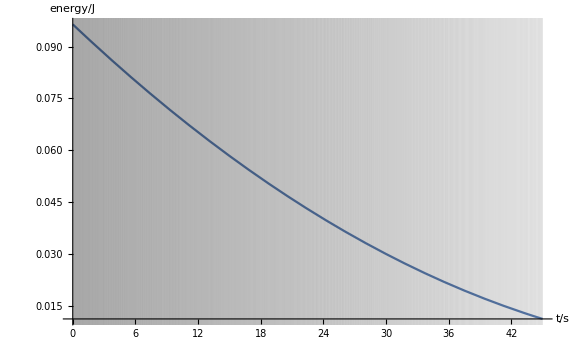

```mathematica
Plot[Evaluate[energy/.Table[α'[t]->D[α[t]/.sol,t],{α,{θ,ϕ,ψ}}]/.para/.sol],{t,0,tmax},
Epilog->{Opacity[.1],PointSize[.005],Table[InfiniteLine[{t,0},{0,1}],{t,periods}]},
PlotRange->All,PerformanceGoal->"Speed",AxesLabel->{"t/s","energy/J"},ImageSize->Large]
```

正压力-时间图

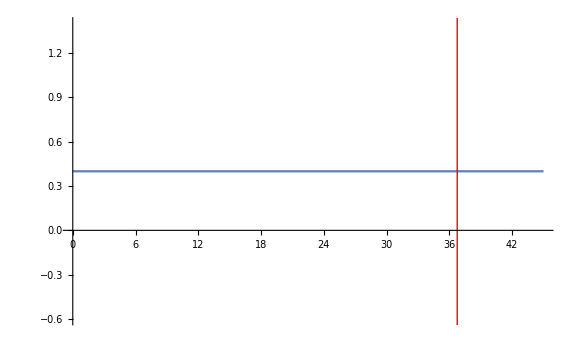

```mathematica
Plot[Evaluate[Subscript[F, N]/.Table[α'[t]->D[α[t]/.sol,t],{α,{θ,ϕ,ψ}}]/.{θ''[t]->D[θ[t]/.sol,{t,2}]}/.para/.sol],{t,0,tmax},Epilog->{Red,Table[InfiniteLine[{t,0},{0,1}],{t,Flatten@errortime}]},PlotRange->All,ImageSize->Large]
```

角加速度（散点平滑）与理论角加速度对比图

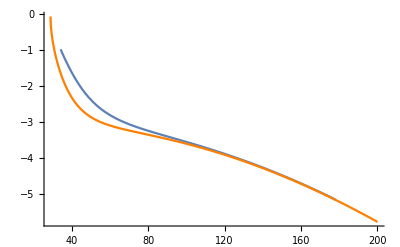

```mathematica
With[{k=200},Show[
ParametricPlot[
Evaluate@{D[ϕ[t]/.sol,t]/.t->tn,
Interpolation[listDerivative[Table[{i,ϕ[t]/.sol/.t->i},{i,0,tmax,.001}],k,2]⟦2k;;-2k⟧][tn]},
{tn,.001 2 k,tmax-.001 2 k},AspectRatio->1/GoldenRatio,PlotRange->{{0,All},{All,0}}],
Plot[Mr (25 ω^4)/(50 g^2 M+98 M R^2 ω^4)/.{θ[t]->ArcCos[2/5-g/(ω^2 R)],ϕ'[t]->ω}/.para,{ω,0,200},PlotStyle->Orange]]
]
```

用于发散检测的绘图：

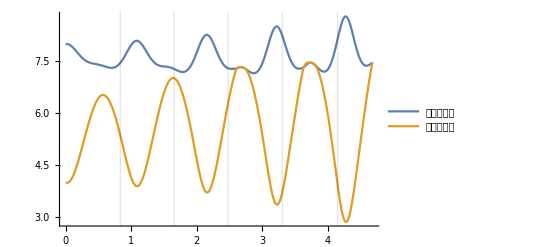

```mathematica
Plot[Evaluate[D[{ϕ[t],ψ[t]}/.sol,t]/.t->tn],{tn,0,Max@@errortime},
Epilog->{Opacity[.1],PointSize[.005],Table[InfiniteLine[{t,0},{0,1}],{t,periods}]},
PlotRange->{0,All},PlotLegends->{"进动角速度","自转角速度"}]
```

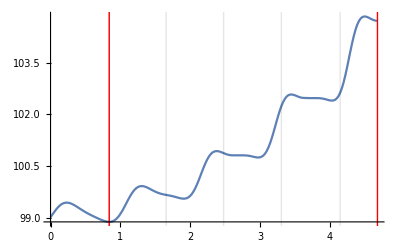

```mathematica
Plot[Evaluate[energy/.Table[α'[t]->D[α[t]/.sol,t],{α,{θ,ϕ,ψ}}]/.para/.sol],{t,0,Max@@errortime},
Epilog->{Opacity[.1],PointSize[.005],Table[InfiniteLine[{t,0},{0,1}],{t,periods}],Red,Opacity@1,Table[InfiniteLine[{t,0},{0,1}],{t,Flatten@errortime}]},
PlotRange->All,PerformanceGoal->"Speed"]
```

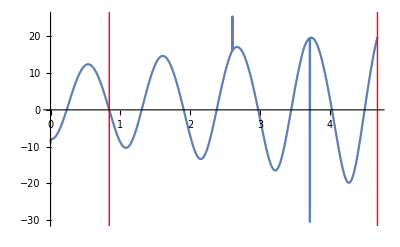

```mathematica
Plot[Evaluate[Subscript[F, N]/.Table[α'[t]->D[α[t]/.sol,t],{α,{θ,ϕ,ψ}}]/.{θ''[t]->D[θ[t]/.sol,{t,2}]}/.para/.sol],{t,0,Max@@errortime},Epilog->{Red,Table[InfiniteLine[{t,0},{0,1}],{t,Flatten@errortime}]},PlotRange->All]
```

初始支持力>0的条件

```mathematica
touchground=FullSimplify[(2M(g+D[R Cos[θ[t]],{t,2}])/.Solve[First@eqns,θ''[t]][[1,1]])>0]
```

M (g (7-5 Sin[θ[t]]^2)-7 R Cos[θ[t]] θ'[t]^2+R Sin[θ[t]]^2 ϕ'[t] (-5 Cos[θ[t]] ϕ'[t]+2 ψ'[t]))>0

```mathematica
Reduce[touchground/.para/.{θ[t]->θ0,θ'[t]->Subscript[ω, θ,0],ϕ'[t]->Subscript[ω, ϕ,0]},ψ'[t]]
```

ψ'[t]>1/16 Sec[23 °]^2 (-7+5 Cos[23 °]^2+320 Cos[23 °]^2 Sin[23 °])

```mathematica
N@Reduce[touchground/.para/.{θ[t]->θ0,θ'[t]->Subscript[ω, θ,0],ϕ'[t]->Subscript[ω, ϕ,0]},ψ'[t]]
```

ψ'[t]>7.61079

```mathematica
Assuming[{π/2>θ[t]>0,ϕ'[t]>0,ψ'[t]>0},Simplify@Reduce[touchground/.para/.{θ'[t]->0},ψ'[t]]]
```

7 Csc[θ[t]]^2+2 ϕ'[t] ψ'[t]>5+5 Cos[θ[t]] ϕ'[t]^2

```mathematica
Manipulate[RegionPlot[%1491/.{θ[t]->θ,ϕ'[t]->Subscript[ω, ϕ],ψ'[t]->Subscript[ω, ψ]},{Subscript[ω, ϕ],0,20},{Subscript[ω, ψ],0,20}],{{θ,66Degree},0,π/2}]
```

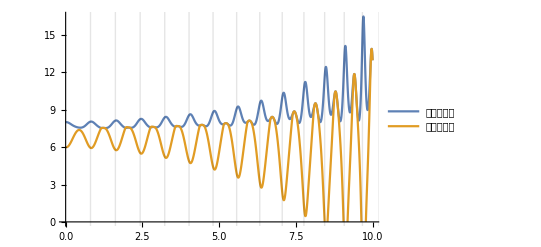

```mathematica
Plot[Evaluate[D[{ϕ[t],ψ[t]}/.sol,t]/.t->tn],{tn,0,10},
Epilog->{Opacity[.1],PointSize[.005],Table[InfiniteLine[{t,0},{0,1}],{t,periods}]},
PlotRange->{0,All},PlotLegends->{"进动角速度","自转角速度"}]
```